```mathematica
path="C:\\Users\\cemh_\\Documents\\Master\\Diamonds\\master-lab-diamonds";
SetDirectory[path];

(*---------------Spectra files----------------*)

Osa001=Import[path<>"\\osa\\001.csv","CSV"]@[[34;;-1]];
Osa002=Import[path<>"\\osa\\002.csv","CSV"][[34;;-1]];
Osa003=Import[path<>"\\osa\\003.csv","CSV"][[34;;-1]];
Osa004=Import[path<>"\\osa\\004.csv","CSV"][[34;;-1]];
```

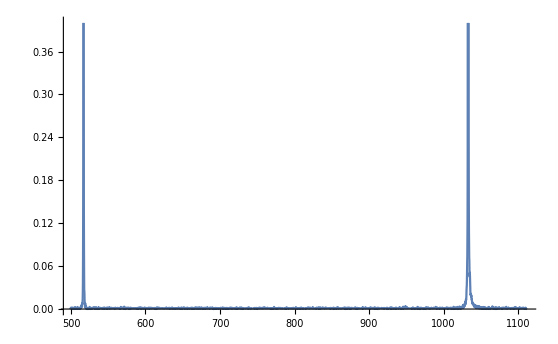

```mathematica
ListLinePlot[Table[Osa001[[x]],{x,1,Length[Osa001]-1}],PlotRange->0.4]
```

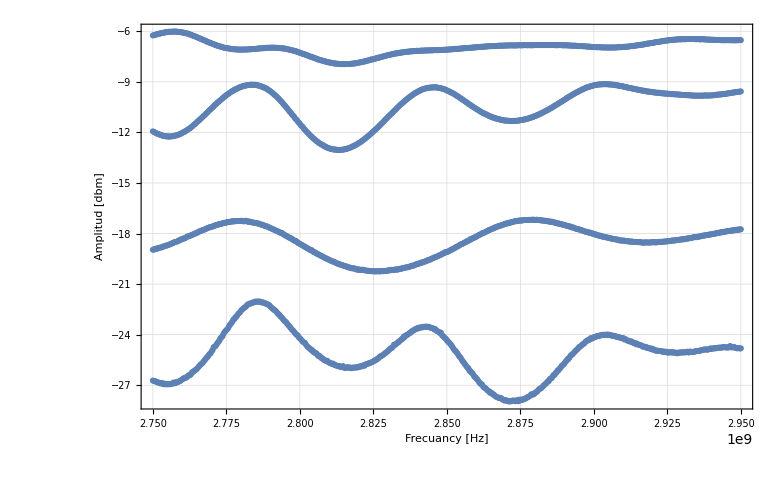

```mathematica
mstrip001=Import[path<>"data\\microstrip\\001.csv","CSV"][[3;;-1,{1,3}]];
mstrip002=Import[path<>"data\\microstrip\\002.csv","CSV"][[3;;-1,{1,3}]];
mstrip003=Import[path<>"data\\microstrip\\003.csv","CSV"][[3;;-1,{1,3}]];
mstrip004=Import[path<>"data\\microstrip\\004.csv","CSV"][[3;;-1,{1,3}]];
legend={"PS Out-In","PS In-Cpl","MS Reflection","MS transmition"};
Show[{ListPlot[mstrip001,PlotTheme->"Detailed"],ListPlot[mstrip002],ListPlot[mstrip003],ListPlot[mstrip004]},PlotRange-> All,AxesLabel-> {"Frecuancy [Hz]","Amplitud [dbm]"},LegendLabel->legend]
```

```mathematica
Pl
```

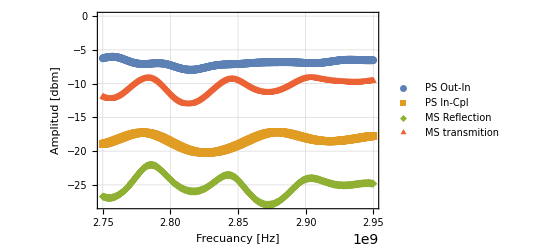

```mathematica
fig1=ListPlot[{mstrip001,mstrip002,mstrip003,mstrip004}, PlotTheme->"Detailed",PlotLegends->legend,FrameLabel->{"Frecuancy [Hz]","Amplitud [dbm]"}, PlotMarkers->{Automatic,8}];
Export[path<>"\\figures\\microstrip.png",fig1,"PNG"];
```

```mathematica
fig2=ListPlot[Partition[Riffle[mstrip001[[All,1]],mstrip004[[All,2]]-(mstrip001[[All,2]])],2],PlotTheme->"Detailed",FrameLabel->{"Frequancy[Hz]","Atenuation[dBm]"},PlotLegends->{"Transmition"},PlotMarkers->{Red,2}];
fig3=ListPlot[Partition[Riffle[mstrip001[[All,1]],mstrip003[[All,2]]+mstrip002[[All,2]]-mstrip001[[All,2]]],2],PlotLegends->{"Reflection"}];
Export[path<>"\\figures\\microstrip-trasm-eflect.png",Show[fig2,fig3,PlotRange -> All],"PNG"]
```

C:\Users\cemh_\Documents\Master\Diamonds\master-lab-diamonds\figures\microstrip-trasm-eflect.png